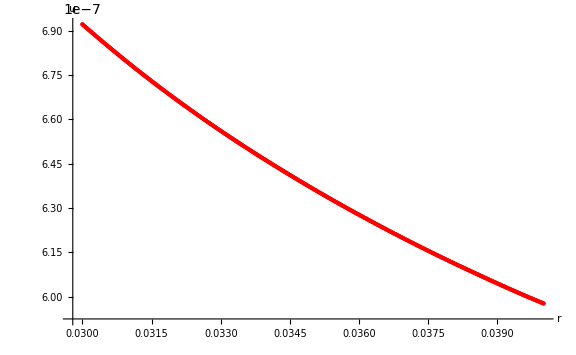

```mathematica
(*ClearAll["Global`*"];*)
SetDirectory[NotebookDirectory[]];
numSolution=ReadList["upr2.txt", {Number, Number}];
settings = ReadList["upr2Settings.txt",Number];
h =settings[[1]];a =settings[[2]];b =settings[[3]];
Pa =settings[[4]];
Pb=settings[[5]];
e=settings[[6]];
nu=settings[[7]];
mu =e/(2(1+nu));
lambda = (nu * e)/((1+nu)(1-2 nu));
exactSol[r_]= (1-2nu)/e*(Pa  a^2-Pb  b^2)/(b^2-a^2)r+(1 + nu)/e * (a^2 b^2)/r * (Pa -Pb)/(b^2-a^2)(*Феодосьев*);
u1=exactSol[0.04];
exactSol[0.03];
plot3 = ListPlot[numSolution , PlotStyle->{Red,Tiny[Large]},PlotTheme->"Classic",AxesLabel->{r,u}, ImageSize->Large];
plot1 =Plot[exactSol[r],{r, a,b},PlotTheme->"Classic",AxesLabel->{r,u},PlotStyle->{Thick, Blue},ImageSize->Large];
Show[plot3, plot, plot2, plot3]
realIntegrate[f_,x_Symbol]:=Simplify[Integrate[f,x]/. Log[expr_]:>Log[Abs[expr]],x∈Reals];
```

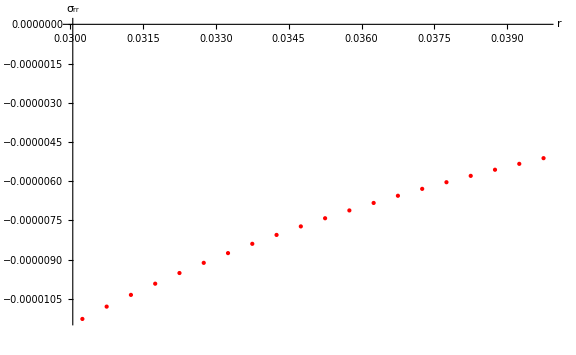

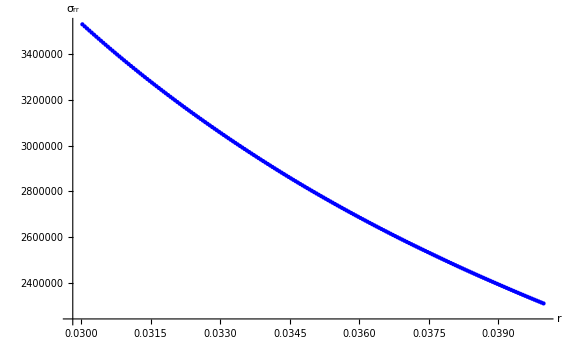

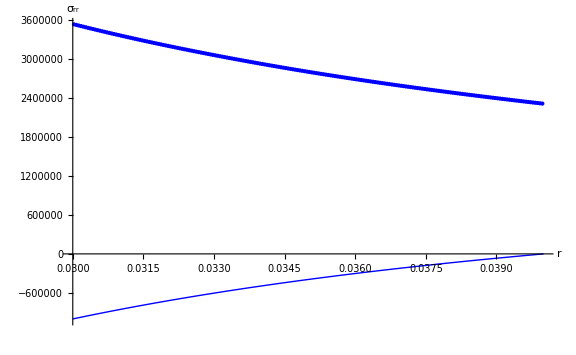

```mathematica
sigmaRR={};
error=0;
exactSigmaRR[r_]= (Pa  a^2-Pb  b^2)/(b^2-a^2)- (a^2 b^2)/r^2 * (Pa -Pb)/(b^2-a^2);

sigmaRR=ReadList["sigmaRR2.txt", {Number, Number}];
p=numSigmaRRPlot=ListPlot[sigmaRR, PlotStyle->{Red,Tiny[Large]},PlotTheme->"Classic",AxesLabel->{r,Subscript[σ, rr]}, ImageSize->Large]
Show[p1, p]
exactSigmaRR[a];
p2=exactSigmaRRPlot=Plot[exactSigmaRR[r],{r, a,b},PlotTheme->"Classic",AxesLabel->{r,Subscript[σ, rr]},PlotStyle->{Thick, Blue},ImageSize->Large, PlotRange->All];
Show[p2,p1]
```

```mathematica
"
```

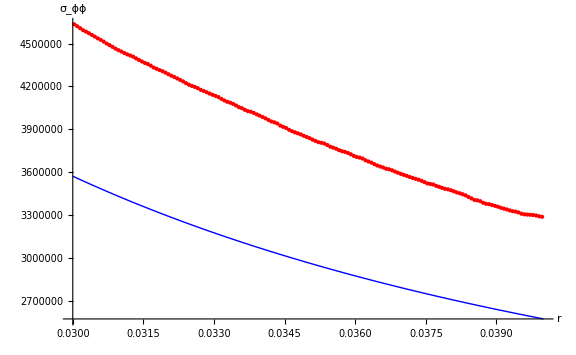

```mathematica
sigmaFF={};
error=0;
exactSigmaFF[r_]= (Pa  a^2-Pb  b^2)/(b^2-a^2)+ (a^2 b^2)/r^2 * (Pa -Pb)/(b^2-a^2);
sigmaFF=ReadList["sigmaFF2.txt", {Number, Number}];
numSigmaFFPlot=ListPlot[sigmaFF, PlotStyle->{Red,Tiny[Large]},PlotTheme->"Classic",AxesLabel->{r,Subscript[σ, ϕϕ]}, ImageSize->Large];
exactSigmaFFPlot=Plot[exactSigmaFF[r],{r, a,b},PlotTheme->"Classic",AxesLabel->{r,Subscript[σ, ϕϕ]},PlotStyle->{Thick, Blue},ImageSize->Large, PlotRange->All];
Show[exactSigmaFFPlot,numSigmaFFPlot]
```